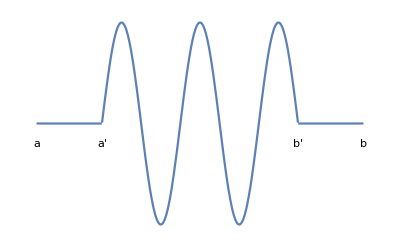

```mathematica
a = -0.2;
test = Plot[Piecewise[{{0,x<0.2},{0,x>0.8},{Sin[(x-0.2)*(5*Pi/0.6)],x≥0.1 &&x≤0.9}}],{x,0,1}, Axes->False];
labels = {Graphics[Text["a",{0,a}]], Graphics[Text["a'",{0.2,a}]], Graphics[Text["b'",{0.8,a}]], Graphics[Text["b",{1,a}]]};
Show[test,labels]
```

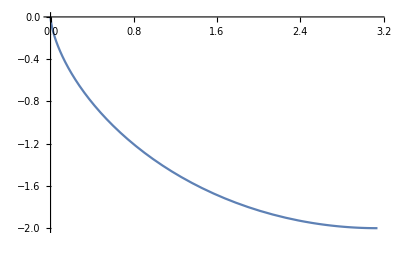

```mathematica
ParametricPlot[{u-Sin[u],Cos[u]-1},{u,0,Pi}]
```